```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
-PowerExpand[Log[Simplify[PDF[ExponentialDistribution[λ],t],t≥0]]]
```

t λ-Log[λ]

```mathematica
(*N0=800;
n0=60;
λ10=3;
λ20=1;
τ0=30;
NN=Length[data];
INTERVAL=1;*)
```

```mathematica
(*data=Flatten[{Table[RandomVariate[ExponentialDistribution[λ10(N0-i+1)]],{i,1,τ0}],Table[RandomVariate[ExponentialDistribution[λ20(N0-j+1)]],{j,τ0+1,n0}]}];*)
```

```mathematica
data=Import["~Downloads/handbooksoftwarereliabilityengineering/DATA/CH4/SYS1.DAT"][[12;;-2]][[;;,2]];
N0=2 Length[data];
data=Table[RandomVariate[ExponentialDistribution[1/3(N0-i+1)]],{i,1,Length[data]}];
```

```mathematica
U[λ1_]=Simplify[Total[Table[PowerExpand[-Log[Simplify[PDF[ExponentialDistribution[λ],t],t≥0]]]/.{t->data[[i]],λ->λ1(N0-i+1)},{i,1,Length[data]}]]](*-((N0-Length[data]) (-t λ1)/.t->Total[data])*);
```

```mathematica
dU[λ1_]=GradientG[U[λ1],{λ1}];
```

```mathematica
ddU[λ1_]=HessianH[U[λ1],{λ1}];
```

```mathematica
INTERVAL=1001;
STEPS=5;
CHAINS=5;
dt10=0.0000000001;
dt20=0.0000000001;
outbnd[q_]:=AnyTrue[q,(#≤0)&];
Dim=1;
qinit=RandomVariate[UniformDistribution[],{CHAINS,Dim}];
QS=hmc[U,dU,ddU,Dim,5000,10000,True,True,qinit];
```

1001-922054.2.490240.2167270.219645-2287.84-924342.-2.27199×10^80.00003200570.00006237True{1,5}{1,6}

2002-1.43223×10^70.003251440.2413270.430988-2286.12-66225.2-1.43246×10^70.0001336960.000286589False{1,4}{1,6}

3003-4031.692.84860.4535220.49956-2285.34-6317.04-823080.0.0003814490.000675761True{2,5,6}{1,6}

4004-35341.70.002503760.4679570.444329-2285.51-3347.7-37627.20.0008176710.00550088False{1,6}{1,6}

5005-207.7872.770520.2299580.432146-2288.38-2496.17-7539.620.001928020.00974514True{1,6}{1,6}

6006-5253.090.001634620.4260190.524893-2286.52-2496.17-7539.620.001928020.00974514False{1,6}{1,6}

7007-211.1062.397390.4741570.43585-2285.06-2496.17-7539.620.001928020.00974514True{1,6}{1,6}

8008-5252.610.003229970.630260.509096-2287.01-2496.17-7539.620.001928020.00974514False{1,6}{1,6}

9009-210.0731.489930.3855390.352147-2286.1-2496.17-7539.620.001928020.00974514True{1,6}{1,6}

```mathematica
QS//Dimensions
```

{25000,1}

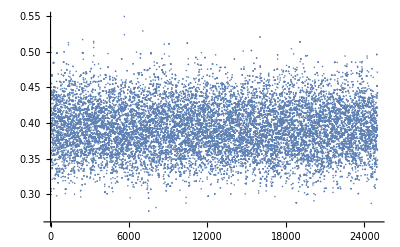

```mathematica
ListPlot[QS[[;;,1]]]
```

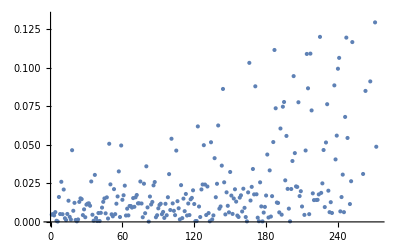

```mathematica
ListPlot[Flatten[{data,Table[RandomVariate[ExponentialDistribution[RandomChoice[QS][[1]](N0-i+1)]],{i,Length[data],2Length[data]}]}]]
```

```mathematica
1/Mean[QS]
```

{2.54735}

```mathematica
Mean[data]//N
```

0.0129289

```mathematica
QS//Dimensions
```

{25000,1}